## Seasonal Ricker model - EWS in rnb - Singles

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tbury/Google Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_seasonal_coe"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=-0.1;
bh=2.24;
```

## Import Data

```mathematica
(* Name of simluation run *)
simName="tmax400_rwp4";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import["data_export/trans_rb/"<>simName<>"/ews_singles.csv"];
```

```mathematica
(* Import power spectrum DataFrame *)
dfPspec=Import["data_export/trans_rb/"<>simName<>"/pspec.csv"];
```

```mathematica
(* Import ews means DataFrame *)
dfEwsMeans=Import["data_export/trans_rb/"<>simName<>"/ews_means.csv"];
```

```mathematica
(* Import ews sd DataFrame *)
dfEwsSd=Import["data_export/trans_rb/"<>simName<>"/ews_deviations.csv"];
```

```mathematica
(* Import Kendall tau values *)
dfKtau=Import["data_export/trans_rb/"<>simName<>"/ktau.csv"];
```

```mathematica
numSims=Length[Union[dfEws[[2;;,1]]]]
```

20

```mathematica
(* Realisation number to display *)
displayNum=1;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* Extract info *)
seriesB = Cases[dfEws[[2;;,{1,2,3,4}]],{displayNum,"Breeding",_,_}][[;;,{3,4}]];
seriesNB = Cases[dfEws[[2;;,{1,2,3,4}]],{displayNum,"Non-breeding",_,_}][[;;,{3,4}]];
(*seriesTotal= Cases[dfEws[[2;;,{1,2,3,4}]],{displayNum,"Total",_,_}][[;;,{3,4}]];*)
```

```mathematica
(* Useful info *)
tVals=seriesB[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
realMax=Max[dfEws[[;;,1]]][[1]];
stateVals=Union[dfEws[[2;;,2]]];
```

```mathematica
(* line legend *)
trajLegend=LineLegend[TMBcolours[[1;;2]],{"Breeding","Non-breeding"},Spacings->{0,0.2},LabelStyle->10]
```

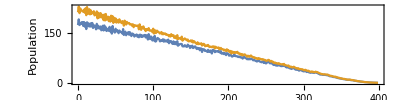

```mathematica
(* plot of breeding series *)
plotPop = ListPlot[{seriesB,seriesNB},
Joined->True,
LabelStyle->12,
PlotLegends->Placed[trajLegend,Scaled[{0.85,0.7}]],
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
AxesLabel->{"t","Population"},
PlotRange->{{0,tmax},All}]
```

### Output

```mathematica
rTicks=Range[bl,bh,0.2];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

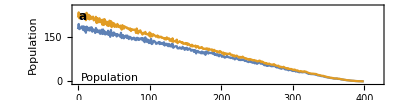

```mathematica
plotTraj=Show[{plotPop},
PlotRange->{{0,tmax*1.05},{-5,250}},
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Breeding growth rate, r_b"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}]}
]
```

## EWS Plots (single realisations)

### Variance

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Variance"][[1,1]];
```

```mathematica
ewsVals=Table[Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}],{state,stateVals}][[;;,;;,{3,4}]];
```

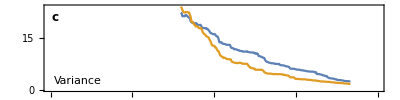

```mathematica
(* Plot EWS *)
plotVar=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}]
```

### Coefficient of variation

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
ewsVals=Table[Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}],{state,stateVals}][[;;,;;,{3,4}]];
```

```mathematica
ewsVals//Dimensions
```

{2,400,2}

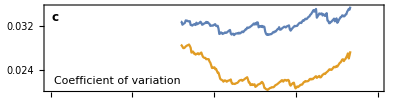

```mathematica
(* Plot EWS *)
plotCv=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

### Smax/Var

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Var"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

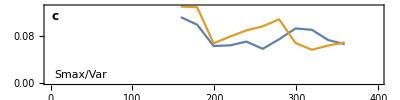

```mathematica
(* Plot EWS *)
plotSmaxVar=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{{"",""},{"Time (generation)",""}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Smax/Var",ls],textPos,{-1,0}]}]
```

### Skewness

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Skewness"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

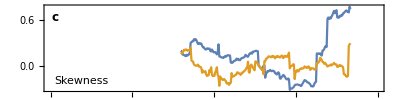

```mathematica
(* Plot EWS *)
plotSkew=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Skewness",ls],textPos,{-1,0}]}]
```

### Kurtosis

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Kurtosis"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

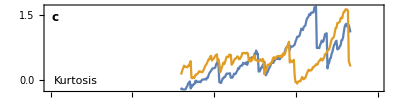

```mathematica
(* Plot EWS *)
plotKurt=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Kurtosis",ls],textPos,{-1,0}]}]
```

### Lag-1 AC

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

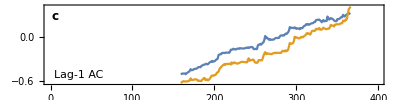

```mathematica
(* Plot EWS *)
plotAc1=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameLabel->{{"",""},{"Time (arbitrary units)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-1 AC",ls],textPos,{-1,0}]}]
```

### Lag-2 AC

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Lag-2 AC"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

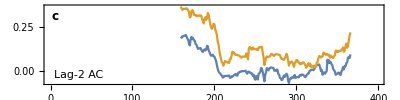

```mathematica
(* Plot EWS *)
plotAc2=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameLabel->{{"",""},{"Time (arbitrary units)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-2 AC",ls],textPos,{-1,0}]}]
```

### Lag-3 AC

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Lag-3 AC"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

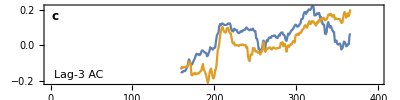

```mathematica
(* Plot EWS *)
plotAc3=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameLabel->{{"",""},{"Time (generation)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-3 AC",ls],textPos,{-1,0}]}]
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

### Variance

```mathematica
indexKtau=Position[dfKtau[[1]],"Variance"][[1,1]]
```

12

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.991453 | -0.984085 | -0.979664 | -0.977306 | -0.979369 | -0.987916 | -0.986148 | -0.983201 | -0.985853 | -0.982611 | -0.98438 | -0.971117 | -0.985853 | -0.97819 | -0.984969 | -0.968759 | -0.98438 | -0.985559 | -0.985559 | -0.987622 | -0.988211 | -0.980253 | -0.986148 | -0.986148 | -0.979075 | -0.97318 | -0.978485 | -0.96817 | -0.974948 | -0.969349 | -0.962275 | -0.980253 | -0.98939 | -0.981727 | -0.984969 | -0.985853 | -0.982022 | -0.990274 | -0.976422 | -0.984674 | -0.970822 | -0.989095 | -0.981727 | -0.986737 | -0.982317 | -0.979959 | -0.960212 | -0.93015 | -0.980253 | -0.963454 | -0.971706 | -0.969938 | -0.97819 | -0.976422 | -0.98939 | -0.960507 | -0.985853 | -0.975243 | -0.992632 | -0.986148 | -0.977011 | -0.98438 | -0.977306 | -0.98379 | -0.984969 | -0.984969 | -0.97377 | -0.976422 | -0.980253 | -0.974948 | -0.983495 | -0.98438 | -0.980548 | -0.983201 | -0.975243 | -0.978485 | -0.989685 | -0.979369 | -0.982611 | -0.979664 | -0.989095 | -0.955202 | -0.987032 | -0.979959 | -0.983201 | -0.980843 | -0.982906 | -0.987916 | -0.971706 | -0.980843 | -0.977601 | -0.985853 | -0.963159 | -0.956676 | -0.987327 | -0.984969 | -0.979664 | -0.980253 | -0.981727 | -0.984674
Non-breeding | -0.979369 | -0.949307 | -0.954318 | -0.974654 | -0.927793 | -0.955202 | -0.977896 | -0.971117 | -0.95756 | -0.970528 | -0.947834 | -0.948423 | -0.919835 | -0.94695 | -0.960507 | -0.867079 | -0.943708 | -0.943118 | -0.972885 | -0.975243 | -0.970822 | -0.923666 | -0.972296 | -0.979369 | -0.906867 | -0.921898 | -0.962865 | -0.895373 | -0.958739 | -0.908046 | -0.975833 | -0.959328 | -0.950486 | -0.969643 | -0.955791 | -0.973475 | -0.938108 | -0.964338 | -0.932213 | -0.957265 | -0.923666 | -0.958149 | -0.946065 | -0.95756 | -0.966991 | -0.942823 | -0.962275 | -0.920719 | -0.895962 | -0.965223 | -0.921014 | -0.951076 | -0.95196 | -0.92013 | -0.975538 | -0.943413 | -0.971117 | -0.963749 | -0.948423 | -0.979959 | -0.916593 | -0.941645 | -0.949013 | -0.980253 | -0.976422 | -0.961981 | -0.974654 | -0.962865 | -0.963454 | -0.95756 | -0.985559 | -0.952255 | -0.949602 | -0.950486 | -0.927793 | -0.983495 | -0.982906 | -0.979664 | -0.963749 | -0.979664 | -0.95756 | -0.952255 | -0.970528 | -0.945771 | -0.974948 | -0.963454 | -0.960212 | -0.979075 | -0.906572 | -0.953434 | -0.958444 | -0.954612 | -0.922782 | -0.944887 | -0.898615 | -0.921014 | -0.959328 | -0.91453 | -0.961391 | -0.939581

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Coefficient of variation

```mathematica
indexKtau=Position[dfKtau[[1]],"Coefficient of variation"][[1,1]]
```

6

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.592101 | 0.359859 | 0.520483 | 0.676098 | 0.922487 | 0.0701444 | 0.345712 | 0.735927 | 0.796051 | 0.684645 | 0.428235 | 0.698792 | 0.848217 | 0.796051 | 0.387857 | 0.920424 | 0.845859 | 0.0277041 | 0.736222 | 0.551429 | 0.0424403 | 0.296788 | 0.147657 | -0.237843 | 0.917477 | 0.924256 | 0.33687 | 0.750958 | 0.375479 | 0.925729 | 0.41674 | 0.753316 | 0.147952 | 0.818744 | 0.464191 | -0.270262 | 0.588859 | 0.47598 | 0.746242 | 0.298851 | 0.883879 | 0.397878 | 0.0450928 | 0.616269 | 0.663425 | 0.857059 | 0.360153 | 0.524315 | 0.789861 | 0.34247 | 0.933098 | 0.676393 | 0.835544 | 0.94636 | 0.669614 | 0.864427 | 0.799587 | 0.632773 | -0.0763336 | 0.776599 | 0.817271 | 0.643383 | 0.63631 | 0.12791 | 0.24079 | -0.501326 | 0.952255 | 0.910698 | 0.571765 | 0.787798 | 0.765694 | 0.50221 | 0.413793 | 0.748305 | 0.859711 | 0.0742706 | -0.383142 | 0.661951 | 0.0975538 | 0.754789 | 0.168877 | 0.56705 | 0.858827 | 0.662835 | 0.835249 | 0.276157 | 0.330681 | 0.0468612 | 0.859122 | 0.913056 | 0.633363 | 0.594164 | 0.87651 | 0.790746 | 0.885352 | 0.391099 | 0.494253 | 0.308871 | 0.73298 | 0.259947
Non-breeding | 0.760094 | 0.521662 | 0.92013 | 0.698792 | 0.531683 | 0.496021 | 0.6313 | 0.86148 | 0.735927 | 0.898025 | 0.825818 | 0.830533 | 0.836723 | 0.889478 | 0.644562 | 0.700855 | 0.916004 | 0.736811 | 0.915709 | 0.886236 | 0.857648 | 0.681108 | 0.724138 | -0.178014 | 0.498084 | 0.926024 | 0.895078 | 0.640731 | 0.510757 | 0.964633 | 0.92514 | 0.629237 | 0.118479 | 0.888299 | 0.54023 | 0.679929 | 0.526083 | 0.880342 | 0.903036 | 0.669614 | 0.950781 | 0.258768 | 0.215149 | 0.912467 | 0.800472 | 0.666961 | 0.92514 | 0.800177 | 0.81285 | 0.868258 | 0.931034 | 0.816092 | 0.648983 | 0.867079 | 0.655467 | 0.820513 | 0.832302 | 0.853522 | 0.747421 | 0.810787 | 0.75361 | 0.720307 | 0.810492 | 0.667551 | 0.841144 | 0.551135 | 0.843207 | 0.937518 | 0.655467 | 0.938108 | 0.451518 | 0.590038 | 0.771589 | 0.870027 | 0.763926 | 0.373121 | 0.681992 | 0.904509 | 0.410256 | 0.862953 | 0.562039 | 0.824344 | 0.850575 | 0.831712 | 0.702623 | 0.482759 | 0.648394 | 0.578544 | 0.588859 | 0.807545 | 0.58827 | 0.6201 | 0.78043 | 0.927203 | 0.808134 | 0.805777 | 0.536104 | 0.223991 | 0.93634 | 0.597112

```mathematica
(* Box plot *)
boxCv=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-1 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-1 AC"][[1,1]]
```

5

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.88771 | 0.733569 | 0.800766 | 0.774241 | 0.811671 | 0.899204 | 0.81285 | 0.953434 | 0.937813 | 0.923961 | 0.782199 | 0.844975 | 0.904804 | 0.879163 | 0.925729 | 0.94135 | 0.891836 | 0.931034 | 0.861185 | 0.925435 | 0.789861 | 0.89272 | 0.916004 | 0.90392 | 0.900678 | 0.839375 | 0.842322 | 0.808429 | 0.881816 | 0.742116 | 0.921014 | 0.893899 | 0.917182 | 0.893015 | 0.905099 | 0.815208 | 0.79723 | 0.939287 | 0.961686 | 0.842912 | 0.875332 | 0.933982 | 0.923077 | 0.870616 | 0.899499 | 0.959917 | 0.921309 | 0.974064 | 0.939581 | 0.845859 | 0.914825 | 0.880637 | 0.906572 | 0.928971 | 0.826997 | 0.885942 | 0.83407 | 0.894783 | 0.863837 | 0.883584 | 0.916004 | 0.820218 | 0.8659 | 0.954318 | 0.954318 | 0.738285 | 0.861185 | 0.959328 | 0.880931 | 0.945771 | 0.867079 | 0.86649 | 0.901267 | 0.93074 | 0.944002 | 0.841438 | 0.938108 | 0.894783 | 0.911583 | 0.605069 | 0.890363 | 0.835838 | 0.933098 | 0.883879 | 0.841144 | 0.852343 | 0.918951 | 0.864132 | 0.881521 | 0.838196 | 0.899499 | 0.888889 | 0.909814 | 0.904215 | 0.86089 | 0.895373 | 0.934276 | 0.875037 | 0.862953 | 0.903036
Non-breeding | 0.94135 | 0.899794 | 0.778367 | 0.894489 | 0.873563 | 0.90952 | 0.919835 | 0.918656 | 0.954907 | 0.92514 | 0.951076 | 0.954023 | 0.956676 | 0.950781 | 0.971706 | 0.937224 | 0.910109 | 0.945181 | 0.931329 | 0.798998 | 0.898025 | 0.960802 | 0.858827 | 0.927793 | 0.944297 | 0.936929 | 0.897731 | 0.931329 | 0.929856 | 0.891836 | 0.921603 | 0.854996 | 0.953434 | 0.88211 | 0.964633 | 0.892426 | 0.877689 | 0.955791 | 0.958149 | 0.723254 | 0.963749 | 0.937518 | 0.965223 | 0.856764 | 0.917182 | 0.936929 | 0.95697 | 0.964633 | 0.961096 | 0.916298 | 0.951665 | 0.920424 | 0.943413 | 0.893604 | 0.964044 | 0.917182 | 0.777188 | 0.958739 | 0.916593 | 0.918361 | 0.91394 | 0.901267 | 0.946655 | 0.941055 | 0.899204 | 0.93015 | 0.95196 | 0.884468 | 0.93015 | 0.946655 | 0.843796 | 0.8771 | 0.906867 | 0.943708 | 0.950192 | 0.956676 | 0.941055 | 0.935455 | 0.96257 | 0.944592 | 0.93634 | 0.948128 | 0.932803 | 0.896257 | 0.929856 | 0.886531 | 0.895373 | 0.960507 | 0.910404 | 0.890363 | 0.900678 | 0.969643 | 0.94636 | 0.853522 | 0.899794 | 0.891247 | 0.938992 | 0.953434 | 0.918951 | 0.969054

```mathematica
(* Box plot *)
boxAc1=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-2 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-2 AC"][[1,1]]
```

4

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.330386 | 0.530799 | 0.739169 | -0.281167 | 0.318008 | 0.103743 | 0.124079 | 0.00559976 | -0.226938 | 0.191571 | -0.172414 | 0.482169 | 0.510168 | 0.354553 | -0.305629 | 0.468612 | -0.349248 | -0.0153257 | -0.168877 | 0.650162 | 0.356322 | 0.464191 | 0.163572 | -0.418214 | 0.288535 | 0.822281 | 0.333628 | 0.284114 | 0.297672 | 0.705276 | 0.111995 | 0.0851754 | 0.395225 | 0.432361 | -0.248747 | 0.583849 | 0.558798 | 0.241085 | -0.0501032 | 0.210139 | 0.475685 | 0.647804 | 0.0135573 | 0.723843 | 0.151488 | 0.7542 | 0.676098 | 0.570881 | 0.515178 | 0.432361 | 0.645447 | 0.542588 | -0.0966696 | 0.759505 | 0.387268 | 0.396994 | -0.00943118 | 0.715591 | 0.655172 | 0.294724 | 0.756852 | 0.365458 | -0.377542 | 0.146773 | -0.208075 | 0.420572 | 0.827291 | 0.413793 | 0.128795 | 0.843207 | -0.574713 | 0.649573 | 0.258179 | 0.100501 | 0.130858 | 0.0159151 | 0.654288 | 0.119069 | -0.229001 | -0.473622 | 0.34807 | 0.82346 | -0.191571 | 0.740053 | -0.0165046 | 0.2458 | 0.459181 | 0.733864 | 0.588859 | -0.296493 | 0.00206307 | 0.264957 | 0.38992 | 0.556734 | 0.578249 | 0.272325 | 0.0259358 | 0.473622 | 0.180371 | 0.771294
Non-breeding | 0.0736811 | -0.113469 | 0.734159 | 0.235485 | -0.00324197 | 0.377837 | 0.622163 | 0.615679 | 0.570292 | 0.637784 | 0.503389 | 0.697318 | 0.660477 | 0.680813 | 0.127026 | 0.568523 | 0.553198 | -0.268199 | 0.793693 | 0.643089 | 0.501916 | 0.318008 | 0.198055 | 0.410256 | 0.218686 | 0.524315 | 0.466844 | 0.411435 | 0.307103 | 0.498968 | 0.71176 | -0.125847 | 0.0966696 | 0.351312 | -0.0978485 | 0.515178 | 0.724138 | 0.557619 | 0.35809 | 0.258179 | 0.90893 | -0.417919 | 0.414383 | 0.730917 | -0.295019 | 0.498084 | 0.762452 | 0.226348 | 0.633658 | 0.640731 | 0.442381 | 0.642499 | 0.608311 | 0.854406 | 0.506926 | 0.415856 | 0.410551 | 0.733864 | 0.463896 | 0.627174 | 0.526378 | 0.0442087 | 0.366637 | -0.0468612 | 0.260536 | 0.435897 | 0.492485 | -0.162688 | -0.173593 | 0.597701 | -0.418214 | -0.049219 | -0.322134 | 0.225464 | -0.116711 | 0.208075 | 0.388742 | -0.205423 | -0.0816387 | 0.709991 | -0.408488 | 0.627763 | -0.500442 | 0.954612 | 0.613322 | 0.564692 | 0.530209 | 0.142057 | 0.752431 | 0.727085 | 0.23519 | -0.247863 | 0.478927 | 0.43295 | 0.678456 | 0.409078 | 0.160625 | 0.616269 | 0.654583 | 0.642205

```mathematica
(* Box plot *)
boxAc2=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-3 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-3 AC"][[1,1]]
```

13

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.173593 | -0.292956 | 0.216622 | 0.859416 | 0.798703 | -0.274388 | 0.541998 | 0.0689655 | 0.830239 | 0.532272 | 0.102859 | 0.35308 | 0.707633 | 0.0554082 | 0.852048 | 0.573239 | 0.0654288 | 0.205128 | 0.649573 | 0.792809 | -0.220749 | 0.268789 | 0.330091 | -0.670793 | 0.6257 | 0.627174 | 0.813734 | 0.715591 | 0.351312 | 0.73239 | 0.379605 | 0.747421 | 0.379016 | 0.515768 | 0.230769 | -0.667551 | 0.0397878 | 0.14972 | 0.731801 | 0.554377 | 0.327734 | 0.41674 | 0.607427 | 0.5084 | 0.324786 | 0.712349 | 0.825523 | 0.787504 | 0.779251 | -0.11789 | 0.872679 | 0.517536 | 0.57265 | 0.442676 | 0.730622 | 0.842617 | 0.515473 | 0.303566 | 0.0666077 | -0.164456 | 0.0783967 | -0.0975538 | 0.640731 | 0.347775 | 0.28883 | 0.170645 | -0.254347 | 0.170056 | 0.516947 | 0.88211 | -0.474212 | 0.284704 | 0.694665 | 0.502505 | -0.41733 | 0.356322 | -0.204833 | 0.278809 | 0.525788 | 0.566166 | -0.533451 | 0.633952 | 0.581786 | 0.590628 | -0.00412614 | 0.399352 | 0.0291777 | -0.0742706 | 0.239906 | 0.622163 | 0.347185 | 0.631889 | 0.718538 | -0.541114 | 0.342175 | -0.0763336 | 0.533451 | 0.716475 | 0.868258 | 0.265841
Non-breeding | 0.830533 | 0.730917 | 0.128795 | 0.461833 | 0.755084 | 0.565871 | -0.222812 | -0.480401 | 0.327144 | -0.625405 | 0.74919 | 0.702328 | -0.0324197 | -0.261126 | 0.779546 | 0.854406 | 0.737695 | 0.760389 | 0.783083 | 0.603596 | -0.489537 | 0.389331 | 0.436192 | -0.121426 | 0.556734 | 0.82346 | 0.79104 | 0.8659 | 0.731211 | 0.533451 | 0.017094 | 0.645447 | 0.670498 | 0.728264 | 0.565281 | -0.403772 | 0.317418 | -0.0742706 | 0.86089 | 0.0848806 | 0.10168 | 0.254347 | 0.536104 | 0.127026 | 0.60389 | 0.664014 | 0.778073 | 0.805482 | 0.714117 | 0.575302 | 0.793398 | 0.509579 | 0.257884 | 0.847627 | 0.710581 | 0.607427 | 0.506926 | 0.434424 | 0.0483348 | 0.0934276 | -0.159741 | -0.338049 | 0.702623 | 0.558798 | -0.125847 | 0.159151 | -0.119069 | -0.142352 | 0.803714 | 0.647215 | 0.170056 | 0.397878 | 0.808134 | 0.357795 | 0.430887 | 0.533451 | 0.0285883 | 0.608901 | 0.613616 | 0.621869 | 0.825228 | 0.646331 | 0.781904 | 0.720307 | 0.638668 | 0.423224 | -0.542588 | 0.758621 | 0.0436192 | 0.555556 | 0.750958 | 0.838491 | 0.438845 | 0.656057 | 0.813439 | -0.567345 | 0.00972591 | 0.797524 | 0.803124 | -0.28883

```mathematica
(* Box plot *)
boxAc3=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Skewness

```mathematica
indexKtau=Position[dfKtau[[1]],"Skewness"][[1,1]]
```

8

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.279988 | 0.367816 | 0.702918 | -0.472443 | 0.595343 | -0.486295 | 0.742706 | 0.465075 | -0.620984 | 0.36369 | 0.193045 | 0.0191571 | -0.244916 | -0.531093 | -0.149425 | -0.28323 | 0.745063 | 0.523431 | -0.699086 | 0.185087 | -0.0542293 | -0.323607 | 0.0294724 | -0.07486 | -0.615385 | 0.303271 | -0.216917 | -0.645741 | 0.55084 | -0.251695 | 0.265547 | 0.473033 | 0.159741 | -0.347185 | 0.508694 | -0.344238 | -0.512821 | 0.382552 | 0.587975 | 0.142057 | -0.471854 | 0.762157 | 0.356322 | 0.511936 | 0.295609 | 0.345712 | 0.558208 | 0.0465665 | 0.488653 | -0.151194 | -0.82346 | 0.2402 | 0.514589 | 0.742411 | -0.18214 | 0.130858 | -0.355143 | -0.178898 | -0.482464 | 0.529915 | 0.692013 | -0.0733864 | -0.353375 | -0.0315355 | -0.126732 | 0.31506 | 0.554082 | 0.687887 | 0.674624 | 0.733569 | 0.179487 | 0.549661 | -0.639847 | -0.0480401 | -0.171824 | 0.315945 | 0.0574713 | 0.402888 | -0.259652 | -0.509873 | 0.22959 | -0.366342 | -0.261715 | 0.75921 | -0.157972 | -0.0421456 | 0.663425 | -0.596817 | 0.266431 | 0.506337 | -0.470085 | 0.565871 | 0.374005 | -0.366342 | -0.339228 | 0.166814 | 0.439434 | 0.478927 | 0.371942 | 0.359859
Non-breeding | -0.177129 | 0.823755 | 0.507515 | 0.763336 | -0.262305 | 0.180666 | 0.390215 | 0.424108 | -0.0324197 | 0.207486 | 0.158856 | -0.102269 | 0.0232832 | 0.406425 | -0.114648 | 0.0624816 | -0.685234 | 0.164162 | 0.040672 | -0.0562924 | 0.584144 | 0.689655 | 0.505452 | 0.48659 | 0.500737 | 0.336281 | -0.100206 | -0.694371 | -0.444739 | -0.15473 | -0.291188 | 0.221927 | 0.218391 | -0.39552 | 0.451223 | -0.728854 | 0.605659 | 0.371942 | 0.554966 | 0.00618921 | 0.327439 | 0.548187 | 0.140289 | -0.270557 | 0.447686 | 0.467138 | 0.779841 | -0.0111995 | 0.361332 | -0.146478 | -0.180961 | -0.478338 | 0.0831123 | 0.281462 | 0.470085 | 0.685529 | -0.474506 | -0.259063 | -0.249042 | 0.318302 | 0.522546 | 0.0489243 | -0.221633 | 0.378721 | 0.550545 | 0.155909 | 0.554966 | 0.762157 | -0.46537 | -0.0960802 | -0.0887121 | 0.424108 | -0.386089 | -0.762747 | -0.547009 | 0.0241674 | -0.507515 | -0.542882 | -0.394341 | 0.141468 | -0.575597 | 0.066313 | 0.519599 | -0.147657 | 0.603301 | 0.664604 | 0.217801 | -0.020336 | 0.285588 | -0.0424403 | 0.158562 | 0.441497 | 0.298556 | -0.300914 | -0.388742 | 0.371942 | 0.128795 | 0.32066 | 0.365458 | 0.302977

```mathematica
(* Box plot *)
boxSkew=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Kurtosis

```mathematica
indexKtau=Position[dfKtau[[1]],"Kurtosis"][[1,1]]
```

9

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.49219 | 0.746242 | 0.543177 | 0.446213 | 0.83466 | -0.134394 | 0.449455 | 0.806366 | 0.303271 | 0.130268 | 0.0660183 | -0.0657235 | 0.767168 | 0.357795 | -0.186266 | 0.943118 | 0.129384 | 0.216917 | 0.83466 | 0.536398 | 0.533746 | 0.470085 | -0.150899 | -0.0928382 | 0.534925 | 0.333923 | -0.504863 | -0.154436 | -0.143236 | 0.794577 | -0.169467 | 0.371058 | 0.360448 | 0.130858 | 0.598291 | -0.16593 | 0.370469 | 0.687592 | -0.0268199 | 0.118184 | 0.876216 | 0.775715 | -0.207486 | 0.773062 | 0.646036 | -0.271441 | -0.260831 | -0.428529 | 0.257294 | -0.323902 | 0.273504 | 0.31064 | 0.634247 | 0.679929 | 0.095196 | 0.163277 | 0.249042 | 0.0365458 | -0.307987 | 0.699086 | 0.543472 | 0.72738 | 0.662541 | 0.334807 | 0.690834 | 0.340701 | 0.890363 | 0.724433 | 0.346301 | 0.583849 | 0.339817 | 0.798114 | 0.0645447 | 0.410551 | -0.286472 | -0.400531 | 0.302093 | 0.594459 | -0.133805 | 0.722959 | 0.408193 | -0.163277 | 0.64132 | -0.164162 | 0.466549 | 0.1341 | 0.0583554 | -0.103154 | 0.607427 | 0.804598 | 0.875921 | -0.0666077 | 0.104038 | 0.59888 | 0.0860595 | 0.139699 | 0.150015 | 0.00442087 | 0.424403 | -0.377542
Non-breeding | 0.354848 | -0.501326 | 0.453286 | 0.758915 | 0.0147362 | -0.383142 | -0.29384 | 0.400825 | 0.398173 | 0.0875332 | -0.260242 | -0.547009 | -0.286177 | -0.358974 | 0.0669024 | -0.135573 | 0.00618921 | 0.106985 | 0.233422 | 0.466254 | 0.18155 | -0.0120837 | -0.0804598 | -0.486001 | -0.443266 | -0.446213 | 0.354259 | 0.546714 | -0.601533 | -0.236958 | 0.501916 | -0.183024 | -0.365753 | 0.798114 | -0.0377247 | 0.127321 | -0.289419 | 0.570881 | 0.455055 | -0.0940171 | -0.233422 | 0.337754 | -0.449749 | 0.764515 | -0.441497 | -0.499558 | 0.515473 | -0.456823 | -0.492485 | 0.270852 | 0.554082 | -0.166814 | 0.0890068 | -0.177424 | -0.426466 | 0.103154 | -0.335396 | -0.350722 | -0.405541 | -0.0760389 | 0.175066 | -0.192455 | 0.581491 | -0.0294724 | 0.430592 | -0.229885 | 0.329502 | 0.794577 | -0.445034 | -0.633363 | 0.218686 | 0.442381 | -0.411435 | 0.843796 | 0.201592 | -0.0937224 | 0.468022 | 0.68995 | 0.2402 | -0.0972591 | 0.00471559 | -0.0509873 | -0.0828176 | -0.0483348 | 0.624226 | 0.607132 | -0.305924 | -0.57707 | -0.00206307 | -0.576481 | -0.27321 | -0.393162 | 0.489243 | 0.619805 | -0.119069 | 0.365753 | -0.489537 | -0.442381 | 0.127026 | -0.66313

```mathematica
(* Box plot *)
boxKurt=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax"][[1,1]]
```

11

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.733333 | -1. | -0.866667 | -1. | -1. | -1. | -1. | -1. | -1. | -0.733333 | -0.866667 | -1. | -1. | -0.333333 | -1. | 0.0666667 | -1. | -0.866667 | -1. | -0.6 | -0.866667 | -1. | -1. | -1. | -1. | -0.2 | -0.6 | -0.866667 | -1. | -0.733333 | -0.866667 | -0.866667 | -0.866667 | -0.866667 | -1. | -1. | -1. | -0.866667 | -1. | -1. | -0.866667 | -1. | -0.733333 | -0.733333 | -1. | -0.866667 | -0.333333 | -0.0666667 | 0.0666667 | -1. | -0.6 | -1. | -0.733333 | -1. | -0.733333 | -1. | -1. | -0.733333 | -0.866667 | -1. | -0.866667 | -1. | -1. | -0.6 | -1. | -1. | -0.866667 | -1. | -0.733333 | -0.333333 | -1. | -1. | -1. | -0.866667 | -0.2 | -1. | -1. | -0.733333 | -1. | -0.866667 | -1. | -1. | -1. | -0.866667 | -0.866667 | -0.866667 | -1. | -0.866667 | -0.6 | -0.866667 | -1. | -0.866667 | -1. | -0.733333 | -0.466667 | -1. | -0.866667 | -0.733333 | -0.733333 | -0.866667
Non-breeding | -1. | -1. | -1. | -0.733333 | -0.733333 | -1. | -0.866667 | -1. | -1. | -0.866667 | -0.866667 | -0.866667 | -1. | 0.2 | -0.866667 | -0.0666667 | -0.466667 | -1. | -0.733333 | -0.6 | -1. | -0.733333 | -0.733333 | -1. | -0.866667 | -0.6 | -1. | -0.733333 | -0.866667 | -0.333333 | -0.866667 | -1. | -0.733333 | -0.6 | -0.866667 | -1. | -0.733333 | -0.333333 | -0.6 | -0.733333 | -0.733333 | -0.866667 | -0.466667 | -0.866667 | -1. | -0.733333 | -0.2 | -0.733333 | 0.866667 | -0.733333 | -1. | -0.6 | -0.866667 | -0.733333 | -0.6 | -0.2 | -1. | 0.733333 | -1. | -1. | -0.866667 | -0.866667 | -0.866667 | -1. | -1. | -0.866667 | -1. | -0.866667 | -0.333333 | -0.6 | -1. | -1. | -1. | -0.0666667 | -0.333333 | -0.733333 | -1. | -1. | -0.866667 | -1. | -0.866667 | -0.866667 | -0.6 | -0.733333 | -0.733333 | -0.866667 | -1. | -0.733333 | -0.333333 | -1. | -0.6 | -0.2 | -0.866667 | 0.2 | 0.866667 | -0.6 | -0.866667 | -0.333333 | -0.866667 | -0.866667

```mathematica
(* Box plot *)
boxSmax=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Var

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax/Var"][[1,1]]
```

14

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.0666667 | 0.6 | 0.466667 | -0.333333 | 0.466667 | 0.2 | 0.0666667 | -0.2 | -0.2 | 0.466667 | -0.2 | 0.866667 | -0.6 | 0.6 | -0.333333 | 1. | 0.866667 | -0.0666667 | 0.733333 | 0.733333 | 0.333333 | 0.6 | 0.333333 | 0.733333 | -0.2 | 0.866667 | 0.2 | 0.466667 | -0.2 | 0.466667 | 0.333333 | -0.0666667 | 0.2 | 0.733333 | 0.2 | 0.333333 | 0.733333 | 0.733333 | 0.333333 | 0.333333 | 0.333333 | 0.466667 | 0.466667 | 0.466667 | -0.0666667 | 0.2 | 0.866667 | 0.733333 | 0.866667 | 0.6 | 0.866667 | 1. | -0.333333 | 0.333333 | 0.733333 | 0.866667 | -0.333333 | 1. | 0.2 | 0.6 | 0.733333 | -0.466667 | -0.333333 | 0.6 | 0.733333 | -0.333333 | 0.733333 | 0.733333 | 0.866667 | 0.866667 | 0.466667 | -0.2 | -0.0666667 | 0.733333 | 0.866667 | -0.0666667 | -0.333333 | 0.2 | -0.0666667 | 0.0666667 | 0.6 | -0.333333 | -0.466667 | 0.333333 | 0.2 | 0.6 | 0.333333 | 0.866667 | 0.6 | -0.6 | 0.0666667 | 0.866667 | -0.333333 | 0.866667 | 0.6 | -0.0666667 | 0.866667 | -0.2 | -0.2 | 0.2
Non-breeding | -0.333333 | -0.2 | 0.2 | 0.6 | 0.2 | -0.6 | 0.733333 | 0.2 | -0.2 | 0.6 | 0.466667 | 0.733333 | 0.466667 | 1. | 0.333333 | 0.6 | 0.2 | -0.6 | 0.2 | 0.733333 | -0.0666667 | 0.2 | -0.0666667 | 0.733333 | -0.0666667 | 0.466667 | -0.0666667 | 0.466667 | 0.0666667 | 0.333333 | 0.866667 | 0.333333 | 0.0666667 | 0.6 | -0.2 | 0.466667 | 0.466667 | 0.6 | 0.733333 | 0.2 | 0.0666667 | -0.2 | 0.733333 | 0.333333 | -0.466667 | 0.0666667 | 0.866667 | 0.866667 | 1. | 0.0666667 | 0.733333 | 0.466667 | 0.6 | 0.866667 | 0.866667 | 0.2 | -0.466667 | 1. | 0.2 | -0.2 | 0.6 | 0.466667 | 0.733333 | 0.333333 | 0.333333 | -0.466667 | -0.0666667 | 0.466667 | 0.733333 | 0.6 | 0.333333 | 0.0666667 | -0.466667 | 1. | 0.333333 | -0.0666667 | 0.733333 | 0.733333 | -0.466667 | 0.2 | -0.333333 | -0.333333 | -0.0666667 | 0.866667 | 0.2 | 0.2 | 0.866667 | 0.466667 | 0.733333 | 0.2 | 0.333333 | 0.466667 | 0.333333 | 0.866667 | 0.866667 | 0.333333 | 0.733333 | 0.2 | 0.2 | -0.333333

```mathematica
(* Box plot *)
boxSmaxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

## Power Spectrum Plot

```mathematica
(* State variable to use for power spectrum plot *)
vblPlot="Breeding";
```

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Organise power spectrum data

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[dfPspec[[2;;,3]]][[1;;-1;;5]]
```

{159.,259.,359.}

```mathematica
Round[plotTimes]
```

{159,259,359}

```mathematica
dfPspec[[1]]
```

{Realisation number,Variable,Time,Frequency,Empirical}

```mathematica
(* Power spectra of display plot *)
specData=Table[
Cases[dfPspec,{displayNum,vblPlot,timeVal,_,_}][[;;,{4,5}]],
{timeVal,plotTimes}];
```

```mathematica
dfPspec[[2]]
```

{1,Non-breeding,159.,-3.14159,1.46872}

```mathematica
(* Power spectra normalised by the variance *)
varianceVals=Table[Cases[dfEws[[2;;,{1,2,3,8}]],{displayNum,vblPlot,Round[time],_}][[1,4]],{time,plotTimes}];
specNormData=specData;
specNormData[[;;,;;,2]]=specNormData[[;;,;;,2]]/varianceVals;
```

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

```mathematica
specData//Dimensions
```

{3,41,2}

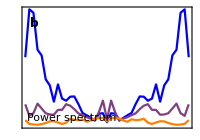

```mathematica
plotPspec=ListLinePlot[specData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

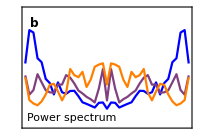

```mathematica
plotPspecNorm=ListLinePlot[specNormData,
PlotRange->{-0.02,0.14},
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Range[-1,1,0.02]},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.75,0.8}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.2cm;
heightBif=3.5cm;
gapVert=0.2cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+7*heightEws+heightBif+7*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotSmaxVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxSmaxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotKurt,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxKurt,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotSkew,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSkew,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotAc2,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxAc2,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th row *)
Inset[Show[plotAc1,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxAc1,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 6th row *)
Inset[Show[plotCv,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+5*heightEws+5*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxCv,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+5*heightEws+5*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 7th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+6*heightEws+6*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+6*heightEws+6*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 8th (top) row  *)
Inset[Show[plotTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+7*heightEws+7*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspecNorm,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+7*heightEws+7*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

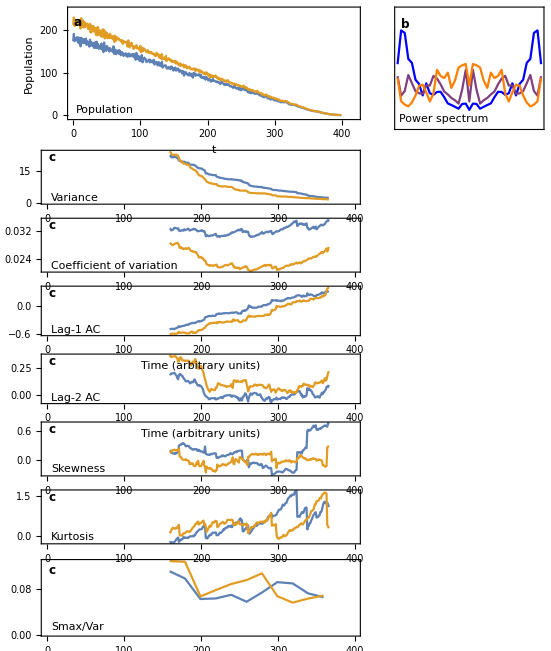

```mathematica
plotGrid
```

```mathematica
Export["figures/ews_trans_rb.png",plotGrid,ImageResolution->200];
```